## Assignment 4

2.1.2(ii)(a-e)

(2)(a) Do the following periodic functions meet the conditions of Theorem 2.1?

(ii)f(x)=3x  on 0<x<2; f(x)=f(x+2).

(b) Find the  Fourier series coefficients A_n and B_n for the periodic functions of part (a).

(c) Plot the resulting series  for different numbers of coefficients M, 1<M<10, and observe the convergence. Compare with the exact functions. Are the series converging?

(d) Plot the difference between the series and the actual functions as M increases, and determine using Eq. (2.1.15) whether the series are exhibiting uniform convergence.

(e) For the series of function (ii), evaluate the derivative of the series with respect to x, term by term.  Compare it with the derivative of 3x on 0<x<2  by plotting the result for M=10, and M=50. Does the derivative of the series give a good representation of f'(x) ?

### Solution

#### (a)

No, the function is discontinuous, as can be seen in a plot of it.

```mathematica
f[x_] := 3 x /; 0<=x≤ 2;
f[x_] := f[x-2] /; x>2;
f[x_] := f[x+2] /; x<0
```

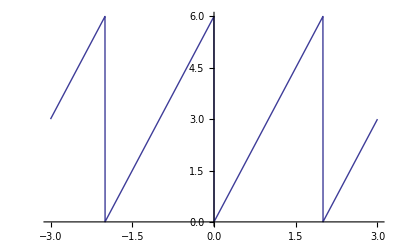

```mathematica
Plot[f[x],{x,-3,3}]
```

#### (b)

```mathematica
T=2;
```

```mathematica
a[n_] = 2/T Integrate[3 x Cos[2 Pi n x/T],{x,0,T}]
```

(3 (-1+Cos[2 n π]+2 n π Sin[2 n π]))/(n^2 π^2)

```mathematica
Simplify[%,n∈ Integers]
```

0

That's interesting, all the a[n]'s are zero. Except for one:

```mathematica
a[0] = Limit[a[n],n->0]/2
```

3

```mathematica
b[n_] = 2/T Integrate[3 x Sin[2 Pi n x/T],{x,0,T}]
```

(3 (-2 n π Cos[2 n π]+Sin[2 n π]))/(n^2 π^2)

```mathematica
FullSimplify[%,n∈ Integers]
```

-6/(n π)

So the b_n's are equal to -6/(n π).

#### (c)

```mathematica
fapprox[x_,M_] := 3 + Sum[(-6/(n Pi)) Sin[n 2Pi x/T],{n,1,M}];
```

```mathematica
Table[Plot[{f[x],fapprox[x,M]},{x,0,2T},PlotLabel-> "M = "<>ToString[M]],{M,2,10,2}];
```

```mathematica
ListAnimate[%]
```

The series is not converging well near the discontinuities, but it is converging OK away from them.

#### (d)

```mathematica
Table[Plot[{f[x]-fapprox[x,M]},{x,0,2T},PlotRange->{-3,3},PlotLabel->"M = "<>ToString[M]],{M,2,10,2}];
ListAnimate[%]
```

The error is not decreasing in magnitude near the discontinuities. This is nonuniform convergence

#### (e)

```mathematica
fapproxprime[x_,M_] := Sum[(-6/(n Pi)) (2 Pi n/T)  Cos[n 2Pi x/T],{n,1,M}];
```

Note that the n's cancel out. The Fourier coefficients no-longer decrease with increasing n. A bad sign.

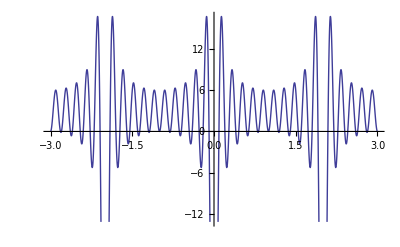

```mathematica
Plot[fapproxprime[x,10],{x,-3,3}]
```

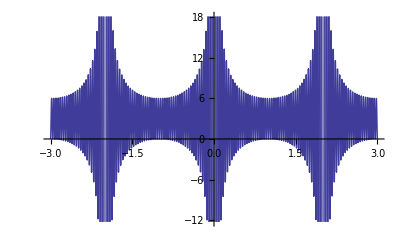

```mathematica
Plot[fapproxprime[x,50],{x,-3,3}]
```

This isn't converging at all! Moral-- be very careful when taking derivatives of a Fourier series term by term! The result is supposed to be a constant,  3 (away from the discontinuities)! Every time you take a derivative of the series, you pull out another factor of n, making the series converge more and more poorly for each derivative taken. For series that don’t converge uniformly in the first place, this can be a disaster.

2.1.4

(4) Repeat Exercise (2)(b) and (c) using exponential Fourier series.

### Solution

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_] := 3x /; 0<=x≤ 2;
f[x_] := f[x-2] /; x>2;
f[x_] := f[x+2] /; x<0
```

```mathematica
T=2;
```

```mathematica
c[n_] = 1/T Integrate[3 x Exp[2 Pi I n x/T],{x,0,2}]
```

(3 (-1+ⅇ^(2 ⅈ n π) (1-2 ⅈ n π)))/(2 n^2 π^2)

```mathematica
c[0] = Limit[c[n],n->0]
```

3

```mathematica
c[n_] = Simplify[c[n],n∈Integers]
```

-(3 ⅈ)/(n π)

```mathematica
fapprox[x_,M_] := Sum[c[n] Exp[-2 Pi I n x/T],{n,-M,M}];
```

```mathematica
Table[Plot[{f[x],fapprox[x,M]},{x,0,2T},PlotLabel-> "M = "<>ToString[M]],{M,2,10,2}];
```

```mathematica
ListAnimate[%]
```

The result is precisely the same as before.

2.1.5

(5) A damped harmonic oscillator satisfies the equation x''+x'+4x=f(t). The forcing function is given by  f(t)=t^2, -1≤ t≤ 1; f(t+2)=f(t).

(a) Find a particular solution x_p(t) to the forcing in terms of an exponential Fourier series.

(b)  Find a homogeneous solution to add to your particular solution from part a) so as to satisfy the ODE with initial conditions  x(0)=1,x'(0)=0. Plot the solution for 0<t<20.

### Solution

#### (a)

The particular solution is of the form x_p(t) = ∑_(n=-∞)^∞ c_n ⅇ^(-ⅈ ω_n t), where ω_n=2 π n/Tand T=2 is the period of the forcing. Each fourier component satisfies 
(-ω_n^2- ι ω_n+4)c_n=f_n where f_n is the Fourier component of f(t) given by

```mathematica
Clear["Global`*"]
```

```mathematica
T=2;
ω[n_] = 2 Pi n/T;
```

```mathematica
f[n_] = FullSimplify[1/T Integrate[Exp[I ω[n] t] t^2,{t,-T/2,T/2}],n∈ Integers]
```

(2 (-1)^n)/(n^2 π^2)

```mathematica
f[0] = 1/T Integrate[Exp[I ω[0] t] t^2,{t,-T/2,T/2}]
```

1/3

```mathematica
c[n_] := f[n]/(-ω[n]^2 - I ω[n] + 4);
```

```mathematica
xp[t_,M_] := Sum[c[n] Exp[-I ω[n] t],{n,-M,M}]
```

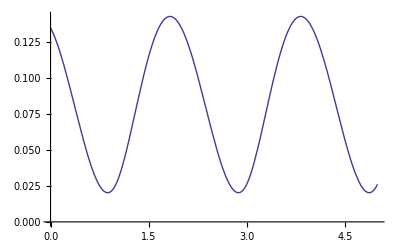

```mathematica
Plot[xp[t,10],{t,0,5}]
```

#### (b)

Homogeneous solution: x = ⅇ^(s t) which implies s^2 + s + 4 =0

```mathematica
Solve[s^2 + s + 4 ==0,s]
```

{{s→1/2 (-1-ⅈ √15)},{s→1/2 (-1+ⅈ √15)}}

So the general homogeneous solution, in terms of sines and cosines, is:

```mathematica
xh[t_] = Exp[-t/2](C1 Cos[ Sqrt[15]t/2] + C2 Sin[Sqrt[15] t/2]);
```

The total solution is:

```mathematica
xtot[t_]  = xp[t,10] + xh[t];
```

(Again, 10 terms in the series is enough for reasonable accuracy).

Now solve for the undetermined constants using the initial conditions

```mathematica
x[t_] = xtot[t]/.Solve[{xtot[0]==1,xtot'[0]==0},{C1,C2}][[1]];
```

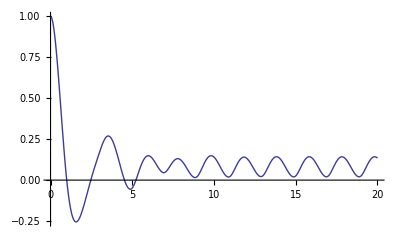

```mathematica
Plot[x[t],{t,0,20},PlotRange->All]
```

2.2.2(c)

(2) Use the periodic extension for the following functions on the given intervals to determine an exponential Fourier series. In each case plot the resulting series, keeping M=20 terms:

(c) f(t)=t^2-1/2,  0<t<1.

### Solution

```mathematica
Clear["Global`*"]
```

```mathematica
f[t_] = t^2 - 1/2;
```

```mathematica
T=1;
Δω = 2 Pi/T;
```

```mathematica
c[n_] = 1/T Integrate[f[t] Exp[I n Δω t],{t,0,T}]
```

-(ⅈ (1+n^2 π^2+ⅇ^(2 ⅈ n π) (ⅈ+n π)^2))/(4 n^3 π^3)

```mathematica
c[0] = Limit[c[n],n->0]
```

-1/6

```mathematica
c[n_] = FullSimplify[c[n],n∈ Integers]
```

(1-ⅈ n π)/(2 n^2 π^2)

```mathematica
fapprox[t_] = Sum[c[n] Exp[-I n Δω t],{n,-20,20}];
```

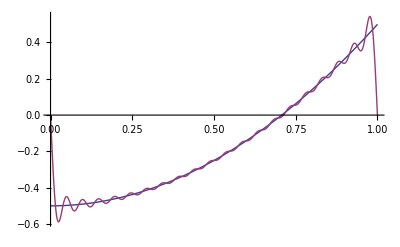

```mathematica
Plot[{f[t],fapprox[t]},{t,0,T}]
```

There is a Gibb’s phenomenon because the periodic extension of the function is not continuous

2.2.3(a,c)

(3) For  case (a) and (c) in Exercise (2) state which type of periodic extension (even or odd) will improve convergence the most. Evaluate the series for the chosen periodic extension with M=20, and plot the result.

### Solution

#### (a)

An odd periodic extension is best, because f(t)  is zero at the endpoints.

```mathematica
Clear["Global`*"]
```

```mathematica
T = Pi;
ω[n_] = 2 Pi n/T;
```

```mathematica
a[n_] = FullSimplify[2/T Integrate[Sin[ω[n] t] Sin[4 t] Exp[t],{t,0,Pi/2}] 2,n∈ Integers]
```

(64 (-1+(-1)^n ⅇ^(π/2)) n)/((289-120 n^2+16 n^4) π)

```mathematica
fapprox[t_] = Sum[a[n] Sin[ω[n] t],{n,1,20}];
```

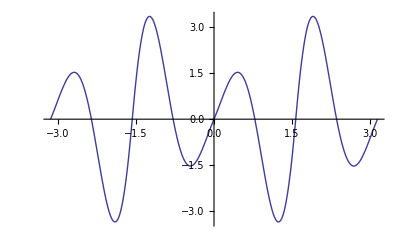

```mathematica
Plot[fapprox[t],{t,-Pi,Pi}]
```

#### (c)

The even periodic extension works better than the odd periodic extension because the function is nonzero at the ends.

```mathematica
Clear["Global`*"]
```

```mathematica
f[t_] = t^2-1/2;
```

```mathematica
T=1; Δω = 2 Pi/T;
```

```mathematica
a[n_] = 2/T Integrate[Cos[n Δω t/2] f[t],{t,0,T}]
```

(4 n π Cos[n π]+(-4+n^2 π^2) Sin[n π])/(n^3 π^3)

```mathematica
a[0] = Limit[a[n],n->0]/2
```

-1/6

```mathematica
a[n_] = FullSimplify[a[n],n∈ Integers]
```

(4 (-1)^n)/(n^2 π^2)

```mathematica
fapproxeven[t_] = Sum[a[n] Cos[n Δω t/2],{n,0,20}];
```

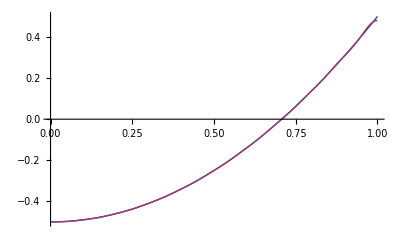

```mathematica
Plot[{f[t],fapproxeven[t]},{t,0,T}]
```

No  Gibb's phenomenon.